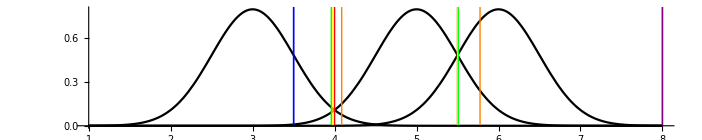

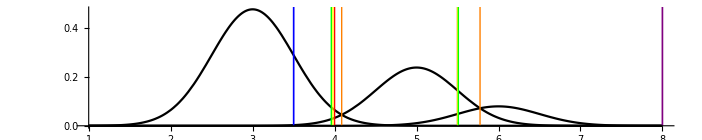

```mathematica
Quiet[Do[
means = {3,5,6};
priors = {0.6,0.3,0.1};
var =0.5;
DecisionRGmean :=Do[
D1=0;D2=0;
max = 0;
Do[
Do[
R1 = CDF[NormalDistribution[means[[1]],var],d1];
R2 = CDF[NormalDistribution[means[[2]],var],d2]- CDF[NormalDistribution[means[[2]],var],d1];
R3= 1 - CDF[NormalDistribution[means[[3]],var],d2];
If[(R1*R2*R3)>max,D1 = d1; D2 = d2;max=(R1*R2*R3),Null];
,{d2,4,7,0.01}];
,{d1,3,5,0.01}];
decision = {};
AppendTo[decision,D1];
AppendTo[decision,D2];
Return[decision],
{1}];
DecisionRHmean :=Do[
D1=0;D2=0;
max = 0;
Do[
Do[
R1 = CDF[NormalDistribution[means[[1]],var],d1];
R2 = CDF[NormalDistribution[means[[2]],var],d2]- CDF[NormalDistribution[means[[2]],var],d1];
R3= 1 - CDF[NormalDistribution[means[[3]],var],d2];
If[(3/(1/R1+1/R2+1/R3))>max,D1 = d1; D2 = d2;max=(3/(1/R1+1/R2+1/R3)),Null];
,{d2,4,7,0.01}];
,{d1,3,5,0.01}];
decision = {};
AppendTo[decision,D1];
AppendTo[decision,D2];
Return[decision],
{1}];
DecisionRMin :=Do[
D1=0;D2=0;
max = 0;
Do[
Do[
R1 = CDF[NormalDistribution[means[[1]],var],d1];
R2 = CDF[NormalDistribution[means[[2]],var],d2]- CDF[NormalDistribution[means[[2]],var],d1];
R3= 1 - CDF[NormalDistribution[means[[3]],var],d2];
If[Min[R1,R2,R3]>max,D1 = d1; D2 = d2;max=Min[R1,R2,R3],Null];
,{d2,4,7,0.01}];
,{d1,3,5,0.01}];
decision = {};
AppendTo[decision,D1];
AppendTo[decision,D2];
Return[decision],
{1}];
G= DecisionRGmean;
H= DecisionRHmean;
M =  DecisionRMin;

F[mu1_,mu2_,eta1_,eta2_,var_]:= var^2/(mu1-mu2)*Log[eta2/eta1]+(mu1+mu2)/2;
Print[Plot[Evaluate@Table[PDF[NormalDistribution[μ,var],x],{μ,means}],{x,1,8}, PlotStyle->{{Black},{Black},{Black}},Epilog -> {Red,Thick,Line[{{4,0},{4,1}}],Line[{{5.5,0},{5.5,1}}],
Orange, Thick,Line[{{F[means[[1]],means[[2]],priors[[1]],priors[[2]],0.5],0},{F[means[[1]],means[[2]],priors[[1]],priors[[2]],0.5],1}}] ,Line[{{F[means[[2]],means[[3]],priors[[2]],priors[[3]],0.5],0},{F[means[[2]],means[[3]],priors[[2]],priors[[3]],0.5],1}}] ,
Yellow,Thick,Line[{{G[[1]],0},{G[[1]],1}}],Line[{{G[[2]],0},{G[[2]],1}}],
Green,Thick,Line[{{H[[1]],0},{H[[1]],1}}],Line[{{H[[2]],0},{H[[2]],1}}],
Blue,Thick,Line[{{M[[1]],0},{M[[1]],1}}],Line[{{M[[1]],0},{M[[1]],1}}],
Purple,Thick,Line[{{8,0},{8,1}}],Line[{{8,0},{8,1}}]},
AspectRatio->1/5]];
Print[Plot[Evaluate@Table[priors[[i]]*PDF[NormalDistribution[means[[i]],0.5],x],{i,{1,2,3}}],{x,1,8}, PlotRange->All,PlotStyle->{{Black},{Black},{Black}},Epilog -> {Red,Thick,Line[{{4,0},{4,1}}],Line[{{5.5,0},{5.5,1}}],
Orange, Thick,Line[{{F[means[[1]],means[[2]],priors[[1]],priors[[2]],0.5],0},{F[means[[1]],means[[2]],priors[[1]],priors[[2]],0.5],1}}] ,Line[{{F[means[[2]],means[[3]],priors[[2]],priors[[3]],0.5],0},{F[means[[2]],means[[3]],priors[[2]],priors[[3]],0.5],1}}] ,
Yellow,Thick,Line[{{G[[1]],0},{G[[1]],1}}],Line[{{G[[2]],0},{G[[2]],1}}],
Green,Thick,Line[{{H[[1]],0},{H[[1]],1}}],Line[{{H[[2]],0},{H[[2]],1}}],
Blue,Thick,Line[{{M[[1]],0},{M[[1]],1}}],Line[{{M[[1]],0},{M[[1]],1}}],
Purple,Thick,Line[{{8,0},{8,1}}],Line[{{8,0},{8,1}}]},AspectRatio->1/5]];
,{1}]]
```